# EBL optical depth calculation

Author: Jie Zhu
Email: jiezhu@cqu.edu.cn

## Functions

### Physical constants and units in SI

```mathematica
c=299792458.;(*m/s*)
h=6.62607015*^-34;(*kg m^2/s*)

eV=1.602176634*^-19;(*eV to J, J*)
keV=1*^3 eV;
MeV=1*^3 keV;
GeV=1*^3 MeV;
TeV=1*^3 GeV;
PeV=1*^3 TeV;
Mpl=1.220890*^19 GeV;

me=0.5110 MeV(*mass of electron*);

um=1*^-6;(*micro meter, m*)
cm=1*^-2;
km=1*^3;
Mpc=3.08567758*^22;(*Mpc to meter,m*)

(*Cosmology parameters*)
Om=0.315;
Ol=0.685;
H0=70*km/1/Mpc;(*km/s/Mpc to 1/s*)

σT=6.6524587321*^-29;(*Thomson cross-section, m^2*)
```

### EBL data import and interpolation

Use the data: EBL intensities from Finke et al. (2022)

```mathematica
dataEBLRaw=Import[FileNameJoin[{NotebookDirectory[],"data","EBL_nuInu_model_A_Finke2022.dat"}],"Table"]//DeleteCases[#,{"#",___}]&;
```

Redshifts:

```mathematica
zTable=dataEBLRaw[[1,2;;-1]];
```

Wavelength, and convert the unit from micrometer to SI unit meter:

```mathematica
λTable=um*dataEBLRaw[[2;;-1,1]];
```

Intensity, and convert the unit from [nW / m^2 / sr] to SI unit [W / m^2 / sr]:

```mathematica
νIνTable=10^-9*dataEBLRaw[[2;;-1,2;;-1]];
```

Convert wavelength to energy in SI unit [J]:

```mathematica
eTable=h c/λTable;
```

Joint intensity Table as: { {λ, z},  νIν}

```mathematica
jointIntensityTable=Flatten[#,1]&@MapThread[List,{Outer[List,λTable,zTable],νIνTable},2];
```

Joint density Table as : { {e, z},  n}

```mathematica
Clear[ToDensity];
ToDensity[{{λ_?NumericQ,z_?NumericQ},i_?NumericQ}]:={{h c /λ, z},4π/c/(h c /λ)^2*i };
```

```mathematica
jointDensityTable=ToDensity/@jointIntensityTable;
```

Density function:

```mathematica
{emin,emax}=MinMax@eTable;
DensityKernel=Interpolation[jointDensityTable];
Density[ϵ_,z_]:=If[emin<ϵ<emax,DensityKernel[ϵ,z],0];
```

Test of density function:

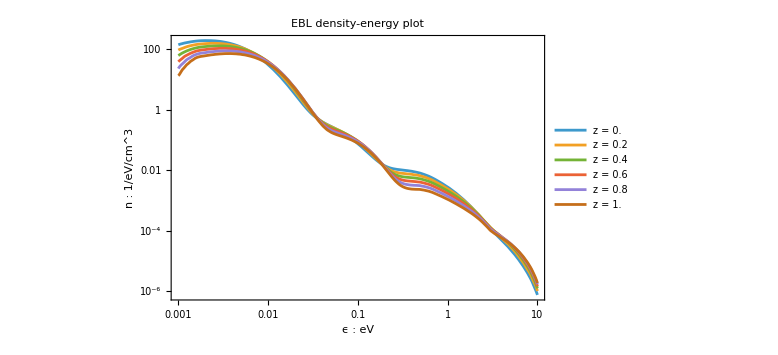

```mathematica
LogLogPlot[
Table[Density[x*eV,z]* eV*cm^3(*1/eV/cm^3*),{z,0,1,0.2}]//Evaluate,{x,1*^-3,10},
Frame->True,
FrameStyle->Directive[Black],
PlotLegends->Placed[
LineLegend[
"z = "<>ToString[#]&/@Range[0,1,0.2],LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->5], 
{Right,Top}],
ImageSize->Large,
FrameLabel->Function[Style[#,Black,16,FontFamily->"Times New Roman"]]/@{"ϵ : eV","n : 1/eV/cm^3"},
PlotLabel->Style["EBL density-energy plot",Black,Bold,20,FontFamily->"Times New Roman"],
GridLines->Automatic
]
```

### Optical depth function

γ +γ -> e^++e^- cross section:

```mathematica
σ[β_]:=3/16σT(1-β^2)(2β(β^2-2)+(3-β^4)Log[(1+β)/(1-β)])
```

Kernel function from http://arxiv.org/abs/1502.04166 :

```mathematica
P[x_]:=Log[2]^2-π^2/6+2 PolyLog[2,(1-x)/2]-(x+x^3)/(1-x^2)+(Log[1+x]-2Log[2])Log[1-x]+1/2(Log[1-x]^2-Log[1+x]^2)+(1+x^4)/(2(1-x^2))Log[(1+x)/(1-x)]
```

#### Optical depth without LV:

```mathematica
dldz[z_]:=1/(1+z)1/(√(Ol+Om(1+z)^3))
```

```mathematica
Clear[OpticalDepth];
Options[OpticalDepth]=Options[NIntegrate];
OpticalDepth[E0_?NumberQ,z0_?NumberQ,opts:OptionsPattern[]]:=3/4(σT c)/H0 NIntegrate[dldz[z]DensityKernel[ϵ,z](me^2/(E0(1+z)ϵ))^2 P[√(1-me^2/(E0(1+z)ϵ))],{z,0,z0},{ϵ,Min[Max[emin,me^2/(E0 (1+z))],emax],emax},Evaluate[FilterRules[{opts},Options[NIntegrate]]]
]//Quiet
```

```mathematica
OpticalDepth[10TeV,0.15]//AbsoluteTiming
```

{0.907658,4.53724}

```mathematica
OpticalDepth[10TeV,0.15,PrecisionGoal->4]//AbsoluteTiming
```

{0.141697,4.53721}

#### Optical depth with LV, from Jacob & Piran http://arxiv.org/abs/0810.1318 .

The MDR for photon is E^2=p^2(1-s (E/E_lv)^n) , where s=+1 means subluminal and -1 means superluminal.

```mathematica
Clear[OpticalDepthJP,Type,ElectronMass];
Type::usage="Type is an option for LV OpticalDepth calculation, Type ->1 or -1, where +1 means subluminal and -1 means superluminal. Type->0 means no LV.";

ElectronMass::usage="ElectronMass is an option for LV OpticalDepth calculation, you can change it to muon mass for example.";

Options[OpticalDepthJP]={Order->1,Type->1,ElectronMass->me,Sequence@@Options[NIntegrate]};
OpticalDepthJP[E0_?NumericQ,z0_?NumericQ,elv_?NumericQ,opts:OptionsPattern[]]:=Module[{n,s,Me},
n=OptionValue[Order];
s=OptionValue[Type];
Me=OptionValue[ElectronMass];
(σT c)/H0 NIntegrate[dldz[z]*DensityKernel[ϵ,z]*3/4*((Me^2/(E0 (1+z))+s (E0(1+z))/4((E0(1+z))/elv)^n)/ϵ)^2 P[√(1-(Me^2/(E0 (1+z))+s (E0(1+z))/4((E0(1+z))/elv)^n)/ϵ)],{z,0,z0},{ϵ,Min[Max[emin,Me^2/(E0 (1+z))+s (E0(1+z))/4((E0(1+z))/elv)^n],emax],emax},
Evaluate[FilterRules[{opts},Options[NIntegrate]]]]
]//Quiet;
```

#### Test:

```mathematica
OpticalDepthJP[10*TeV,0.15,0.3*Mpl,PrecisionGoal->3]//AbsoluteTiming
```

{0.090091,3.58574}

```mathematica
OpticalDepthJP[10*TeV,0.15,0.3*Mpl]//AbsoluteTiming
```

{0.814661,3.58589}

To speed up the calculation, PrecisionGoal option helps.

#### The new optical depth with LV, from calculation of the cross section

```mathematica
Clear[MyIntPart1,IntPart,IntPart1,IntPart2];
(*MyIntPart1[ϵ_,E0_,z_,elv_,n_:1,s_:1,Me_:me]:=Module[{A,B,βmax},
A=Me^2/(ϵ E0 (1+z));
B=-s((E0(1+z))/elv)^n(E0 (1+z))/(2ϵ);
βmax=√(1-(2A)/(2+B));
Return[1/(8 (-1+βmax^2))3 A^2 (2 (βmax+βmax^3)-Log[1-βmax]^2+Log[1+βmax]^2+(1+βmax^4+Log[4]+βmax^2 Log[1/4 (1-βmax^2)]) Log[-1+2/(1+βmax)]+2 (-1+βmax^2) PolyLog[2,(1-βmax)/2]-2 (-1+βmax^2) PolyLog[2,(1+βmax)/2])]
];*)
IntPart1[ϵ_,E0_,z_,elv_,n_:1,s_:1,Me_:me]:=Module[{A,B,βmax},
A=Me^2/(ϵ E0 (1+z));
B=-s((E0(1+z))/elv)^n(E0 (1+z))/(2ϵ);
βmax=√(1-(2A)/(2+B));
Return[3/4 A^2 P[βmax]]
];
IntPart2[ϵ_,E0_,z_,elv_,n_:1,s_:1,Me_:me]:=Module[{A,B,βmax},
A=Me^2/(ϵ E0 (1+z));
B=-s((E0(1+z))/elv)^n(E0 (1+z))/(2ϵ);
βmax=√(1-(2A)/(2+B));
Return[-3/16 A B (7 βmax-βmax^3+Log[1-βmax]^2-Log[1+βmax]^2+1/2 (-7+2 βmax^2+βmax^4+Log[16]) (-Log[1-βmax]+Log[1+βmax])+2 PolyLog[2,(1-βmax)/2]-2 PolyLog[2,(1+βmax)/2])]
]
(*IntPart[ϵ_,E0_,z_,elv_,n_:1,s_:1,Me_:me]:=IntPart1[ϵ,E0,z,elv,n,s,Me]+IntPart2[ϵ,E0,z,elv,n,s,Me]*)
IntPart[ϵ_,E0_,z_,elv_,n_:1,s_:1,Me_:me]:=Module[{A,B,βmax,t1,t2},
A=Me^2/(ϵ E0 (1+z));
B=-s((E0(1+z))/elv)^n(E0 (1+z))/(2ϵ);
βmax=√(1-(2A)/(2+B));
t1=3/4 A^2 P[βmax];
t2=-3/16 A B (7 βmax-βmax^3+Log[1-βmax]^2-Log[1+βmax]^2+1/2 (-7+2 βmax^2+βmax^4+Log[16]) (-Log[1-βmax]+Log[1+βmax])+2 PolyLog[2,(1-βmax)/2]-2 PolyLog[2,(1+βmax)/2]);
Return[t1+t2]
]
```

Compared to Jacob & Piran:

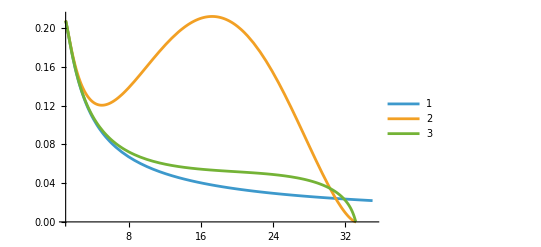

```mathematica
Plot[{3/4((Me^2/(E0 (1+z)))/ϵ)^2 P[√(1-(Me^2/(E0 (1+z)))/ϵ)],3/4((Me^2/(E0 (1+z))+s (E0(1+z))/4((E0(1+z))/elv)^n)/ϵ)^2 P[√(1-(Me^2/(E0 (1+z))+s (E0(1+z))/4((E0(1+z))/elv)^n)/ϵ)],
IntPart[ϵ,x TeV,z,elv]}/.{ϵ->1eV,E0->x TeV,z->0.15,elv->0.03Mpl,Me->me,s->1,n->1}//Evaluate,{x,1,35},PlotLegends->Range[5]]
```

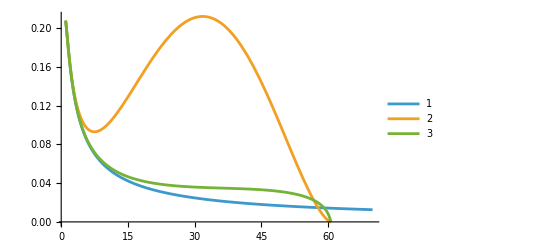

```mathematica
Plot[{3/4((Me^2/(E0 (1+z)))/ϵ)^2 P[√(1-(Me^2/(E0 (1+z)))/ϵ)],3/4((Me^2/(E0 (1+z))+s (E0(1+z))/4((E0(1+z))/elv)^n)/ϵ)^2 P[√(1-(Me^2/(E0 (1+z))+s (E0(1+z))/4((E0(1+z))/elv)^n)/ϵ)],
IntPart[ϵ,x TeV,z,elv]}/.{ϵ->1eV,E0->x TeV,z->0.15,elv->0.1Mpl,Me->me,s->1,n->1}//Evaluate,{x,1,70},PlotLegends->Range[5]]
```

There are differences!

```mathematica
Clear[OpticalDepthMy];
Options[OpticalDepthMy]=Options[OpticalDepthJP];
OpticalDepthMy[E0_?NumericQ,z0_?NumericQ,elv_?NumericQ,opts:OptionsPattern[]]:=Module[{n,s,Me},
n=OptionValue[Order];
s=OptionValue[Type];
Me=OptionValue[ElectronMass];
(σT c)/H0 NIntegrate[dldz[z]DensityKernel[ϵ,z]IntPart[ϵ,E0,z,elv,n,s,Me],{z,0,z0},{ϵ,Min[Max[emin,Me^2/(E0 (1+z))+s (E0(1+z))/4((E0(1+z))/elv)^n],emax],emax},
Evaluate[FilterRules[{opts},Options[NIntegrate]]]]
]//Quiet;
```

### Tests:

```mathematica
OpticalDepthJP[10*TeV,0.15,Mpl,PrecisionGoal->3]//AbsoluteTiming
```

{0.091558,4.1835}

```mathematica
OpticalDepthJP[10*TeV,0.15,Mpl]//AbsoluteTiming
```

{0.927818,4.18412}

```mathematica
OpticalDepthMy[10*TeV,0.15,Mpl,PrecisionGoal->3]//AbsoluteTiming
```

{0.115278,4.15637}

```mathematica
OpticalDepthMy[10*TeV,0.15,Mpl]//AbsoluteTiming
```

{1.15532,4.15713}

```mathematica
OpticalDepthMy[10*TeV,0.15,Mpl,Type->0]
```

4.53724

```mathematica
OpticalDepth[10*TeV,0.15]
```

4.53724

## Examples

```mathematica
energyListTeV=PowerRange[10^-2,10^2.5,10.^(4.5/200)];
elvListMpl={0.03,0.1,1,10};
```

```mathematica
taoNoLV=ParallelMap[{#,Exp[-OpticalDepth[#*TeV,0.15,PrecisionGoal->3]]}&,energyListTeV];
```

### Jacob & Piran method:

To speedup the calculation, set the PrecisionGoal option for NIntegrate:

```mathematica
taoJPList=Table[Echo[i];ParallelMap[{#,Exp[-OpticalDepthJP[#*TeV,0.15,i*Mpl,PrecisionGoal->3]]}&,energyListTeV],
{i,elvListMpl}];
```

0.03

0.1

1

10

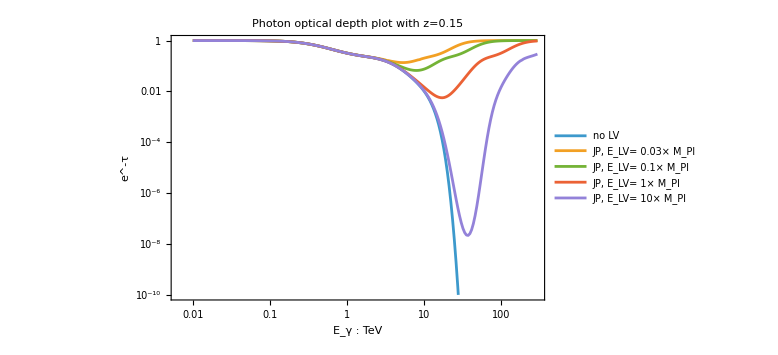

```mathematica
plotJP=ListLogLogPlot[Prepend[taoJPList,taoNoLV],
Frame->True,
ImageSize->Large,
PlotRange->{10^-10,0},
Joined->True,
PlotLegends->Placed[LineLegend[Prepend["JP, E_LV= "<>ToString[#]<>"× M_Pl"&/@elvListMpl,"no LV"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5], {Left,Bottom}],
GridLines->Automatic,
FrameStyle->Black,
FrameLabel->Function[Style[#,Black,16,FontFamily->"Times New Roman"]]/@{"E_γ : TeV","e^-τ"},
PlotLabel->Style["Photon optical depth plot with z=0.15",Black,Bold,16,FontFamily->"Times New Roman"]
]
```

### My method:

```mathematica
taoMyList=Table[Echo[i];ParallelMap[{#,Exp[-OpticalDepthMy[#*TeV,0.15,i*Mpl,PrecisionGoal->3]]}&,energyListTeV],
{i,elvListMpl}];
```

0.03

0.1

1

10

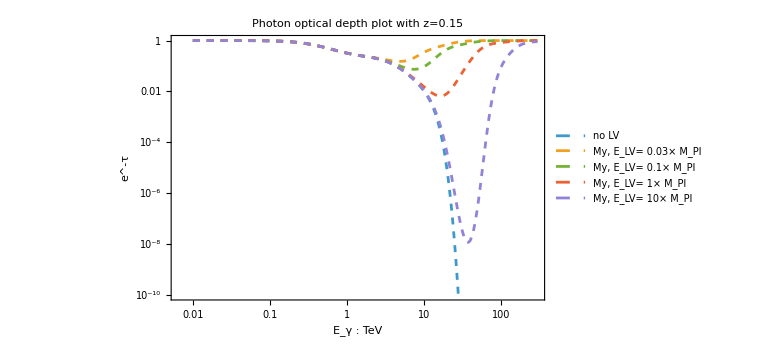

```mathematica
plotMy=ListLogLogPlot[Prepend[taoMyList,taoNoLV],
Frame->True,
ImageSize->Large,
PlotRange->{10^-10,0},
Joined->True,
PlotLegends->Placed[LineLegend[Prepend["My, E_LV= "<>ToString[#]<>"× M_Pl"&/@elvListMpl,"no LV"],LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5], {Left,Bottom}],
GridLines->Automatic,
FrameStyle->Black,
FrameLabel->Function[Style[#,Black,16,FontFamily->"Times New Roman"]]/@{"E_γ : TeV","e^-τ"},
PlotLabel->Style["Photon optical depth plot with z=0.15",Black,Bold,16,FontFamily->"Times New Roman"],
PlotStyle->Dashed
]
```

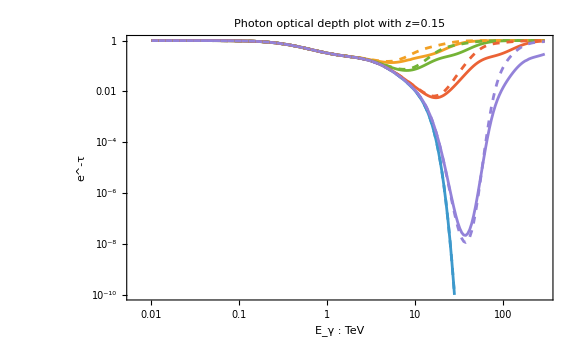

```mathematica
Show[plotJP,plotMy]
```